The source for this notebook is available at https://github.com/gphanikumar/tpnotes

# Elementary plane flows

In this notebook, we look at elementary plane flows that can be described using simple potential  functions. The velocity profiles are obtained by the gradient of potentials.
u=-(∂ϕ)/(∂x) and v=-(∂ϕ)/(∂y)  or u⃗=-OverVector[∇]ϕ
We use coordinate transformation where necessary before plotting.

## Uniform flow

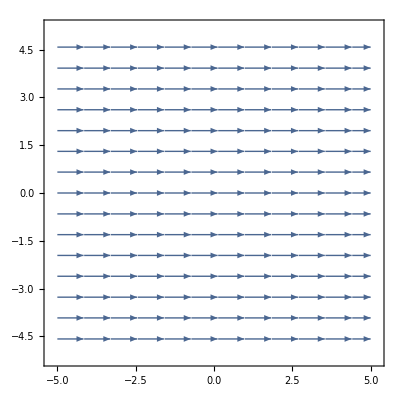

```mathematica
ϕ1[x_,y_]:=-2x;
v1=-Grad[ϕ1[x,y],{x,y}];
StreamPlot[v1,{x,-5,5},{y,-5,5}]
```

## Source flow

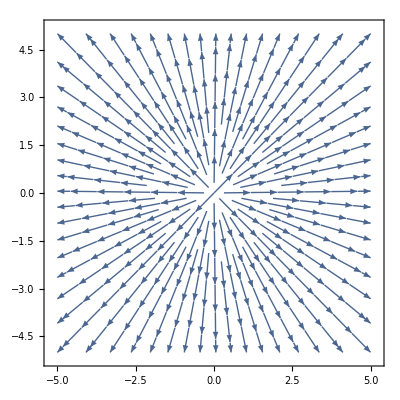

```mathematica
ϕ2[r_,θ_]:=- Log[r]/(2 Pi);
v2=-Grad[ϕ2[r,θ],{r,θ},"Polar"];
v2xy=TransformedField["Polar"->"Cartesian",v2,{r,θ}->{x,y}]//Simplify;
StreamPlot[v2xy,{x,-5,5},{y,-5,5}]
```

## Sink flow

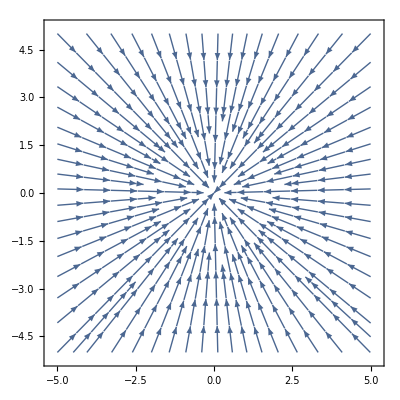

```mathematica
ϕ3[r_,θ_]:= Log[r]/(2 Pi);
v3=-Grad[ϕ3[r,θ],{r,θ},"Polar"];
v3xy=TransformedField["Polar"->"Cartesian",v3,{r,θ}->{x,y}]//Simplify;
StreamPlot[v3xy,{x,-5,5},{y,-5,5}]
```

## Irrotational vortex

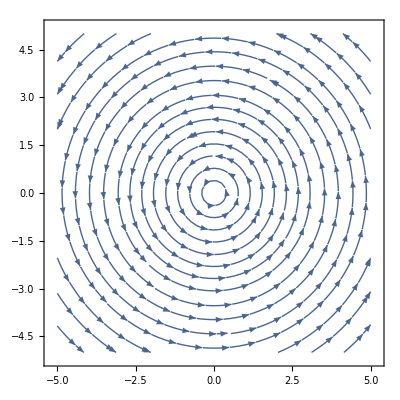

```mathematica
ϕ4[r_,θ_]:= -θ/(2 Pi);
v4=-Grad[ϕ4[r,θ],{r,θ},"Polar"];
v4xy=TransformedField["Polar"->"Cartesian",v4,{r,θ}->{x,y}]//Simplify;
StreamPlot[v4xy,{x,-5,5},{y,-5,5}]
```

## Doublet

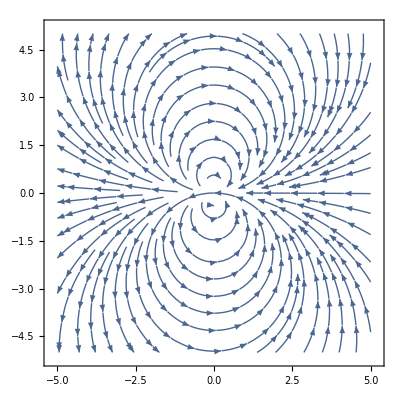

```mathematica
ϕ5[r_,θ_]:= -2 Cos[θ]/(r);
v5=-Grad[ϕ5[r,θ],{r,θ},"Polar"];
v5xy=TransformedField["Polar"->"Cartesian",v5,{r,θ}->{x,y}]//Simplify;
StreamPlot[v5xy,{x,-5,5},{y,-5,5}]
```

```mathematica
Stagnation Flow
```

Flow Stagnation

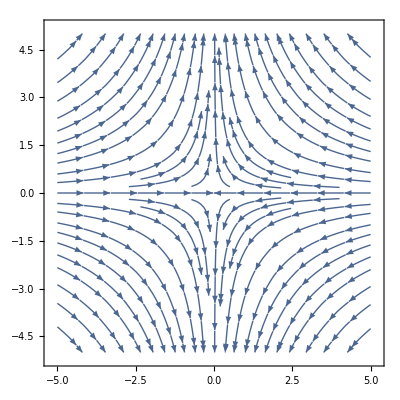

```mathematica
ϕ11[x_,y_]:= x^2- y^2;
v11=-Grad[ϕ11[x,y],{x,y},"Cartesian"];
StreamPlot[v11,{x,-5,5},{y,-5,5}]
```

## Source and uniform flow This pattern will look like flow past a half-body. Change the constants to adjust the the strength of the flow.

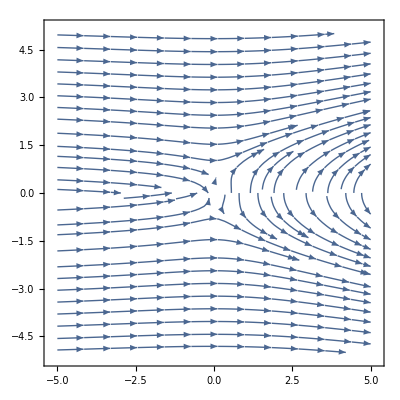

```mathematica
ϕ6[r_,θ_]:= -2Log[θ]-3r Cos[θ];
v6=-Grad[ϕ6[r,θ],{r,θ},"Polar"];
v6xy=TransformedField["Polar"->"Cartesian",v6,{r,θ}->{x,y}]//Simplify;
StreamPlot[v6xy,{x,-5,5},{y,-5,5}]
```

## Doublet, Vortex and uniform flow

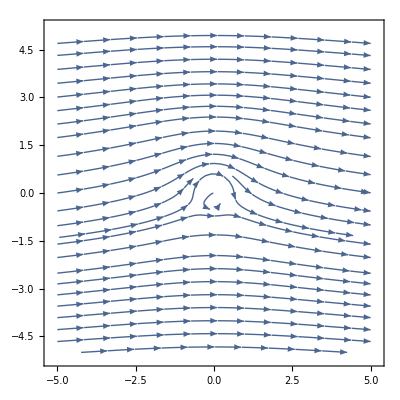

```mathematica
ϕ7[r_,θ_]:= 2θ-3r Cos[θ]- Cos[θ]/(r);
v7=-Grad[ϕ7[r,θ],{r,θ},"Polar"];
v7xy=TransformedField["Polar"->"Cartesian",v7,{r,θ}->{x,y}]//Simplify;
StreamPlot[v7xy,{x,-5,5},{y,-5,5}]
```

## Doublet and uniform flow This pattern simulates flow past a cylinder.

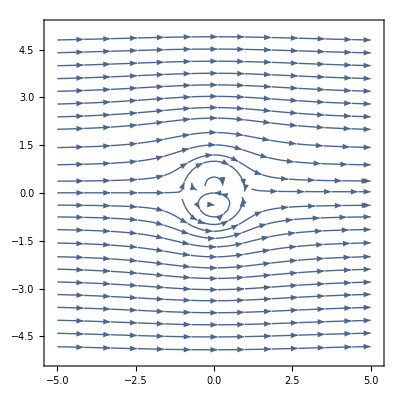

```mathematica
ϕ8[r_,θ_]:= -2r (1+1/r^2)Cos[θ];
v8=-Grad[ϕ8[r,θ],{r,θ},"Polar"];
v8xy=TransformedField["Polar"->"Cartesian",v8,{r,θ}->{x,y}]//Simplify;
StreamPlot[v8xy,{x,-5,5},{y,-5,5}]
```

## Doublet, vortex and uniform flow This pattern simulates flow past a cylinder with circulation.

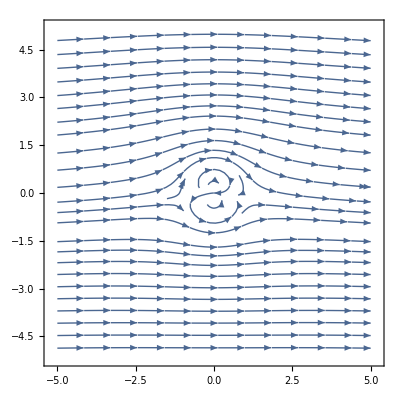

```mathematica
ϕ9[r_,θ_]:= -2r (1+1/r^2)Cos[θ]+ 4θ/(2 Pi);
v9=-Grad[ϕ9[r,θ],{r,θ},"Polar"];
v9xy=TransformedField["Polar"->"Cartesian",v9,{r,θ}->{x,y}]//Simplify;
StreamPlot[v9xy,{x,-5,5},{y,-5,5}]
```

## Source and vortex This pattern simulates a spiral vortex.

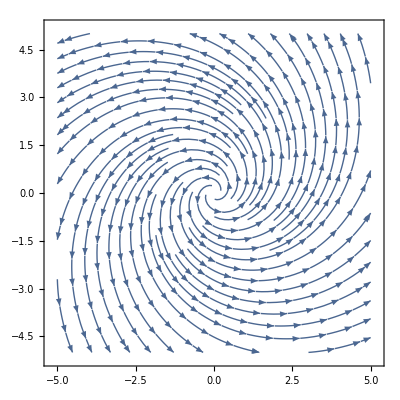

```mathematica
ϕ10[r_,θ_]:= -2Log[r]-4θ;
v10=-Grad[ϕ10[r,θ],{r,θ},"Polar"];
v10xy=TransformedField["Polar"->"Cartesian",v10,{r,θ}->{x,y}]//Simplify;
StreamPlot[v10xy,{x,-5,5},{y,-5,5}]
```